# Ejercicio I.3: Simulación de elementos de la red

## Nombre del Alumno: Felix Sanz González DNI: 78997168B

# -Graphics-

# 1.- Generacion de paquetes, y transmisiones. Abstracción de un enlace

```mathematica
ClearAll;
err = 0.1;
npaquetes = 1000;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
```

1/6000

1066.67

```mathematica
RndExp[ratio_] := -Log[RandomReal[]]/ratio//N;
```

```mathematica
RndExp[lambda]
```

0.000729119

```mathematica
GetArrivals[transmisionlista_,tp_]:=Map[(If[#[[4]]==0,#[[1]]+#[[2]]+tp,Unevaluated[Sequence[]]])&,transmisionlista];
```

```mathematica
(*Source[tentrellegadas_,len_,idFlow_,period_,idIn_:0]:=*)
createPackets[lambda_,len_,idFlow_,period_,idIn_]:= 
Module[{checktime =0, n =1, lista = {idIn}},
NestWhileList[({checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime})&, 
{checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime}, (#[[1]]< period)&]];
```

```mathematica
paquetes = createPackets[lambda,l,1,10,0];
paquetes[[1;;5]]
```

{{0.000272571,1394.09,1,0,0,1,1,{0},0.000272571},{0.000649334,81.5765,2,0,0,2,1,{0},0.000649334},{0.000706978,9.1238,3,0,0,3,1,{0},0.000706978},{0.000807157,1301.5,4,0,0,4,1,{0},0.000807157},{0.00100148,346.481,5,0,0,5,1,{0},0.00100148}}

```mathematica
(* pkt={chkTime,length,nseqLink,error,nrtx,nseqFlow,flowId,{path},{timePath}} *)

createTx[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
None;
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]

createTxSW[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
];

createTxGBN[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c);n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]
```

```mathematica
paquetesNormales = createTx[paquetes,p,TpSW,c];
```

```mathematica
paquetesNormales⟦1;;5⟧
```

{{0.000272571,1394.09,1,0,0,1,1,{0},0.000272571},{0.00104156,81.5765,2,0,0,2,1,{0},0.000649334},{0.00140038,9.1238,3,0,0,3,1,{0},0.000706978},{0.00173657,1301.5,4,0,0,4,1,{0},0.000807157},{0.00247662,346.481,5,0,0,5,1,{0},0.00100148}}

```mathematica
paquetesSW = createTxSW[paquetes,p,TpSW,c];
paquetesSW[[1;;5]]
```

{{0.000272571,1394.09,1,1,0,1,1,{0},0.000272571},{0.00104156,1394.09,1,0,1,1,1,{0},0.000272571},{0.00181055,81.5765,2,0,0,2,1,{0},0.000649334},{0.00216937,9.1238,3,0,0,3,1,{0},0.000706978},{0.00250556,1301.5,4,0,0,4,1,{0},0.000807157}}

```mathematica
paquetesGBN = createTxGBN[paquetes,p,TpSW,c];
paquetesGBN[[1;;5]]
```

{{0.000272571,1394.09,1,0,0,1,1,{0},0.000272571},{0.000708225,81.5765,2,1,0,2,1,{0},0.000649334},{0.00106705,81.5765,2,0,1,2,1,{0},0.000649334},{0.00109254,9.1238,3,0,0,3,1,{0},0.000706978},{0.00109539,1301.5,4,0,0,4,1,{0},0.000807157}}

```mathematica
Get["C:\\Users\\felix\\Desktop\\Todo\\U.P.V\\MASTER\\Segundo\\Asignaturas\\Rendimiento en Redes de Telecomunicacion\\Casos\\Caso I\\drawTxPRM2024.m"];
```

```mathematica
?drawTxPRM2024`*
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesNormales]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesSW]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.005 en WW*)
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesGBN]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.004 en WW*)
```

```mathematica
(*Tenemos que conseguir hacer una lista de paquetes que no contenga los paquetes erroneos --> Filtrar *)
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

```mathematica
paquetesbuenosNormales = filtrarPaquetes[paquetesNormales,c,TpSW];
paquetesNormales[[1;;20]]
paquetesbuenosNormales[[1;;20]]
paquetesbuenosSW = filtrarPaquetes[paquetesSW,c,TpSW];
paquetesSW[[1;;20]]
paquetesbuenosSW[[1;;20]]
paquetesbuenosGBN = filtrarPaquetes[paquetesGBN,c,TpSW];
paquetesGBN[[1;;20]]
paquetesbuenosGBN[[1;;10]]
```

{{0.000272571,1394.09,1,0,0,1,1,{0},0.000272571},{0.00104156,81.5765,2,0,0,2,1,{0},0.000649334},{0.00140038,9.1238,3,0,0,3,1,{0},0.000706978},{0.00173657,1301.5,4,0,0,4,1,{0},0.000807157},{0.00247662,346.481,5,0,0,5,1,{0},0.00100148},{0.00291823,509.471,6,0,0,6,1,{0},0.00150146},{0.00341077,828.074,7,0,0,7,1,{0},0.00251633},{0.00400288,555.901,8,0,0,8,1,{0},0.00286163},{0.00450993,1514.4,9,0,0,9,1,{0},0.00412211},{0.00554865,1262.69,10,0,0,10,1,{0},0.00554865},{0.00642155,200.964,11,0,0,11,1,{0},0.00642155},{0.00692765,1015.18,12,0,0,12,1,{0},0.00692765},{0.00757823,238.11,13,0,0,13,1,{0},0.00734921},{0.00813528,1750.23,14,0,0,14,1,{0},0.00813528},{0.00907241,301.057,15,0,0,15,1,{0},0.00907241},{0.00949983,234.314,16,0,0,16,1,{0},0.00907784},{0.00990638,79.9232,17,0,0,17,1,{0},0.00934197},{0.0102647,142.894,18,0,0,18,1,{0},0.00943939},{0.0106427,201.199,19,0,0,19,1,{0},0.00972315},{0.0110389,330.263,20,0,0,20,1,{0},0.00985076}}

{{0.000874892,1394.09,1,0,0,1,1,{0},0.000272571},{0.00123372,81.5765,2,0,0,2,1,{0},0.000649334},{0.0015699,9.1238,3,0,0,3,1,{0},0.000706978},{0.00230995,1301.5,4,0,0,4,1,{0},0.000807157},{0.00275156,346.481,5,0,0,5,1,{0},0.00100148},{0.00324411,509.471,6,0,0,6,1,{0},0.00150146},{0.00383621,828.074,7,0,0,7,1,{0},0.00251633},{0.00434326,555.901,8,0,0,8,1,{0},0.00286163},{0.00514985,1514.4,9,0,0,9,1,{0},0.00412211},{0.00610991,1262.69,10,0,0,10,1,{0},0.00554865},{0.00665102,200.964,11,0,0,11,1,{0},0.00642155},{0.00741156,1015.18,12,0,0,12,1,{0},0.00692765},{0.0078193,238.11,13,0,0,13,1,{0},0.00734921},{0.0088489,1750.23,14,0,0,14,1,{0},0.00813528},{0.00933316,301.057,15,0,0,15,1,{0},0.00907241},{0.00973972,234.314,16,0,0,16,1,{0},0.00907784},{0.010098,79.9232,17,0,0,17,1,{0},0.00934197},{0.010476,142.894,18,0,0,18,1,{0},0.00943939},{0.0108722,201.199,19,0,0,19,1,{0},0.00972315},{0.0113088,330.263,20,0,0,20,1,{0},0.00985076}}

{{0.000272571,1394.09,1,1,0,1,1,{0},0.000272571},{0.00104156,1394.09,1,0,1,1,1,{0},0.000272571},{0.00181055,81.5765,2,0,0,2,1,{0},0.000649334},{0.00216937,9.1238,3,0,0,3,1,{0},0.000706978},{0.00250556,1301.5,4,0,0,4,1,{0},0.000807157},{0.00324561,346.481,5,0,0,5,1,{0},0.00100148},{0.00368722,509.471,6,0,0,6,1,{0},0.00150146},{0.00417976,828.074,7,0,0,7,1,{0},0.00251633},{0.00477187,555.901,8,0,0,8,1,{0},0.00286163},{0.00527892,1514.4,9,1,0,9,1,{0},0.00412211},{0.0060855,1514.4,9,1,1,9,1,{0},0.00412211},{0.00689208,1514.4,9,1,2,9,1,{0},0.00412211},{0.00769867,1514.4,9,1,3,9,1,{0},0.00412211},{0.00850525,1514.4,9,0,4,9,1,{0},0.00412211},{0.00931183,1262.69,10,0,0,10,1,{0},0.00554865},{0.0100398,200.964,11,0,0,11,1,{0},0.00642155},{0.0104359,1015.18,12,0,0,12,1,{0},0.00692765},{0.0110865,238.11,13,0,0,13,1,{0},0.00734921},{0.0114942,1750.23,14,1,0,14,1,{0},0.00813528},{0.0123745,1750.23,14,1,1,14,1,{0},0.00813528}}

{{0.00164388,1394.09,1,0,1,1,1,{0},0.000272571},{0.0020027,81.5765,2,0,0,2,1,{0},0.000649334},{0.00233889,9.1238,3,0,0,3,1,{0},0.000706978},{0.00307894,1301.5,4,0,0,4,1,{0},0.000807157},{0.00352055,346.481,5,0,0,5,1,{0},0.00100148},{0.00401309,509.471,6,0,0,6,1,{0},0.00150146},{0.0046052,828.074,7,0,0,7,1,{0},0.00251633},{0.00511225,555.901,8,0,0,8,1,{0},0.00286163},{0.00914517,1514.4,9,0,4,9,1,{0},0.00412211},{0.00987309,1262.69,10,0,0,10,1,{0},0.00554865},{0.0102692,200.964,11,0,0,11,1,{0},0.00642155},{0.0109198,1015.18,12,0,0,12,1,{0},0.00692765},{0.0113275,238.11,13,0,0,13,1,{0},0.00734921},{0.0139684,1750.23,14,0,2,14,1,{0},0.00813528},{0.0143958,301.057,15,0,0,15,1,{0},0.00907241},{0.0148024,234.314,16,0,0,16,1,{0},0.00907784},{0.015519,79.9232,17,0,1,17,1,{0},0.00934197},{0.016275,142.894,18,0,1,18,1,{0},0.00943939},{0.0166712,201.199,19,0,0,19,1,{0},0.00972315},{0.0175442,330.263,20,0,1,20,1,{0},0.00985076}}

{{0.000272571,1394.09,1,0,0,1,1,{0},0.000272571},{0.000708225,81.5765,2,1,0,2,1,{0},0.000649334},{0.00106705,81.5765,2,0,1,2,1,{0},0.000649334},{0.00109254,9.1238,3,0,0,3,1,{0},0.000706978},{0.00109539,1301.5,4,0,0,4,1,{0},0.000807157},{0.00150211,346.481,5,0,0,5,1,{0},0.00100148},{0.00161039,509.471,6,0,0,6,1,{0},0.00150146},{0.00251633,828.074,7,0,0,7,1,{0},0.00251633},{0.00286163,555.901,8,0,0,8,1,{0},0.00286163},{0.00412211,1514.4,9,0,0,9,1,{0},0.00412211},{0.00554865,1262.69,10,0,0,10,1,{0},0.00554865},{0.00642155,200.964,11,0,0,11,1,{0},0.00642155},{0.00692765,1015.18,12,1,0,12,1,{0},0.00692765},{0.00757823,1015.18,12,0,1,12,1,{0},0.00692765},{0.00789547,238.11,13,1,0,13,1,{0},0.00734921},{0.00830321,238.11,13,1,1,13,1,{0},0.00734921},{0.00871095,238.11,13,0,2,13,1,{0},0.00734921},{0.00878536,1750.23,14,0,0,14,1,{0},0.00813528},{0.00933231,301.057,15,0,0,15,1,{0},0.00907241},{0.00942639,234.314,16,0,0,16,1,{0},0.00907784}}

{{0.000874892,1394.09,1,0,0,1,1,{0},0.000272571},{0.00125921,81.5765,2,0,1,2,1,{0},0.000649334},{0.00126206,9.1238,3,0,0,3,1,{0},0.000706978},{0.00166878,1301.5,4,0,0,4,1,{0},0.000807157},{0.00177706,346.481,5,0,0,5,1,{0},0.00100148},{0.00193626,509.471,6,0,0,6,1,{0},0.00150146},{0.00294177,828.074,7,0,0,7,1,{0},0.00251633},{0.00320201,555.901,8,0,0,8,1,{0},0.00286163},{0.00476203,1514.4,9,0,0,9,1,{0},0.00412211},{0.00610991,1262.69,10,0,0,10,1,{0},0.00554865}}

# 2 y 3.- Abstracción de un nodo de conmutación. Funciones de filtrado y multiplexado de paquetes.

Debemos implementar una función que nos permita eliminar los paquetes que contienen error, segun el campo de paquete que indica si es un paquete con error

```mathematica
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

Debemos implementar una función que nos permita dividir y conmutar  el trafico entrante a un nodo por sus distintos enlaces de salida. 
Está función tiene como parámetros de entrada la lista de paquetes, las probabilidades de los enlaces de salida y los enlaces de salida

```mathematica
(*Esta funcion da error y NO SE USA*)
Node1[in_,probs_]:=Module[{cumulativeProbs,outcomes,nProbs,nGroups,r,assignedGroups},(*Verificar que las probabilidades sumen 1*)If[Total[probs]!=1,Return["Error: La suma de las probabilidades debe ser 1."]];
(*Calcular los límites acumulados de las probabilidades*)
cumulativeProbs=Accumulate[probs];
(*Número de probabilidades y número de grupos*)
nProbs=Length[probs];
nGroups=nProbs;
(*Asignar cada elemento de'in' a un grupo según probabilidades acumuladas*)
assignedGroups=Map[With[{r=RandomReal[]},FirstPosition[cumulativeProbs,_?(#>=r&)][[1]],in];
(*Mostrar valores aleatorios y asignaciones para depuración*)
Print["Valores aleatorios: ",r,Length[in]]];
Print["Grupos asignados: ",assignedGroups];
(*Crear la lista de resultados agrupados*)
outcomes=Table[Select[Transpose[{in,assignedGroups}],#[[2]]==i+1&][[All,1]],{i,1,Length[probs]}];
(*Devolver los resultados agrupados por etiquetas*)
outcomes]
```

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId} *)
(*Esta es la función que se usa*)

Node2[in_,prob_]:=Reap[
Map[If[RandomReal[]<prob,Sow[#,1],Sow[#,2]]&,in],
_,#2&][[2]];
```

Debemos implementar una función que nos permita multiplexar el trafico entrante a un nodo, para asi obtener una unica lista, ordenada segun el instante de llegada de cada paquete.

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId,{path} *)
Multiplexar[in_,idNodo_]:=Module[{aux={},aux2={},nodes={},times={}},
aux=Flatten[in,1]; (*Concatenar listas de paquetes en una sola lista*)
aux=SortBy[aux,#[[1]]&]; (*Ordenar la nueva lista en base al tiempo en el que han llegado los paquetes al nodo*)
Map[{

nodes=#[[8]];(*Extraer los nodos por los que ha pasado el paquete actual*)
AppendTo[nodes,idNodo]; (*Agregar el nodo actual a la lista de nodos por los que ha pasado el paquete actual*)

AppendTo[aux2,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],nodes,#[[9]]}]}&,aux]; (*Crea la nueva lista de paquetes*)
	aux2
];
```

```mathematica
{enlace1,enlace2}= Node2[paquetesbuenosNormales[[1;;15]],0.5];
Flatten[{enlace1,enlace2},1]
enlace1
enlace2
```

{{0.000874892,1394.09,1,0,0,1,1,{0},0.000272571},{0.00123372,81.5765,2,0,0,2,1,{0},0.000649334},{0.0015699,9.1238,3,0,0,3,1,{0},0.000706978},{0.00324411,509.471,6,0,0,6,1,{0},0.00150146},{0.00383621,828.074,7,0,0,7,1,{0},0.00251633},{0.00434326,555.901,8,0,0,8,1,{0},0.00286163},{0.00665102,200.964,11,0,0,11,1,{0},0.00642155},{0.00933316,301.057,15,0,0,15,1,{0},0.00907241},{0.00230995,1301.5,4,0,0,4,1,{0},0.000807157},{0.00275156,346.481,5,0,0,5,1,{0},0.00100148},{0.00514985,1514.4,9,0,0,9,1,{0},0.00412211},{0.00610991,1262.69,10,0,0,10,1,{0},0.00554865},{0.00741156,1015.18,12,0,0,12,1,{0},0.00692765},{0.0078193,238.11,13,0,0,13,1,{0},0.00734921},{0.0088489,1750.23,14,0,0,14,1,{0},0.00813528}}

{{0.000874892,1394.09,1,0,0,1,1,{0},0.000272571},{0.00123372,81.5765,2,0,0,2,1,{0},0.000649334},{0.0015699,9.1238,3,0,0,3,1,{0},0.000706978},{0.00324411,509.471,6,0,0,6,1,{0},0.00150146},{0.00383621,828.074,7,0,0,7,1,{0},0.00251633},{0.00434326,555.901,8,0,0,8,1,{0},0.00286163},{0.00665102,200.964,11,0,0,11,1,{0},0.00642155},{0.00933316,301.057,15,0,0,15,1,{0},0.00907241}}

{{0.00230995,1301.5,4,0,0,4,1,{0},0.000807157},{0.00275156,346.481,5,0,0,5,1,{0},0.00100148},{0.00514985,1514.4,9,0,0,9,1,{0},0.00412211},{0.00610991,1262.69,10,0,0,10,1,{0},0.00554865},{0.00741156,1015.18,12,0,0,12,1,{0},0.00692765},{0.0078193,238.11,13,0,0,13,1,{0},0.00734921},{0.0088489,1750.23,14,0,0,14,1,{0},0.00813528}}

```mathematica
in2 = Multiplexar[{enlace1,enlace2},A]
```

{{0.000874892,1394.09,1,0,0,1,1,{0,A},0.000272571},{0.00123372,81.5765,2,0,0,2,1,{0,A},0.000649334},{0.0015699,9.1238,3,0,0,3,1,{0,A},0.000706978},{0.00230995,1301.5,4,0,0,4,1,{0,A},0.000807157},{0.00275156,346.481,5,0,0,5,1,{0,A},0.00100148},{0.00324411,509.471,6,0,0,6,1,{0,A},0.00150146},{0.00383621,828.074,7,0,0,7,1,{0,A},0.00251633},{0.00434326,555.901,8,0,0,8,1,{0,A},0.00286163},{0.00514985,1514.4,9,0,0,9,1,{0,A},0.00412211},{0.00610991,1262.69,10,0,0,10,1,{0,A},0.00554865},{0.00665102,200.964,11,0,0,11,1,{0,A},0.00642155},{0.00741156,1015.18,12,0,0,12,1,{0,A},0.00692765},{0.0078193,238.11,13,0,0,13,1,{0,A},0.00734921},{0.0088489,1750.23,14,0,0,14,1,{0,A},0.00813528},{0.00933316,301.057,15,0,0,15,1,{0,A},0.00907241}}

```mathematica
(*Esta funcion permite añadir numeros de secuencia a los paquetes de un flujo, es decir, a los paquetes que ya se sabe que van por un enlace*)
añadirNumSec[lista_,max_]:=Table[Append[lista[[i]],Mod[i-1,max]],{i,1,Length[lista]}]
```

```mathematica
añadirNumSec[enlace1,4]
```

{{0.000874892,1394.09,1,0,0,1,1,{0},0.000272571,0},{0.00123372,81.5765,2,0,0,2,1,{0},0.000649334,1},{0.0015699,9.1238,3,0,0,3,1,{0},0.000706978,2},{0.00324411,509.471,6,0,0,6,1,{0},0.00150146,3},{0.00383621,828.074,7,0,0,7,1,{0},0.00251633,0},{0.00434326,555.901,8,0,0,8,1,{0},0.00286163,1},{0.00665102,200.964,11,0,0,11,1,{0},0.00642155,2},{0.00933316,301.057,15,0,0,15,1,{0},0.00907241,3}}

# 4A.- Simulación de transmisión de paquetes en la topología de red SIN protocolo

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1 = createPackets[lambda,l,1,10,"Ori-1"];
in5 = createPackets[lambda,l,1,10,"Ori-5"];
in2 = createPackets[lambda,l,1,10,"Ori-2"];
in1[[1;;15]];
totalin = Length[in1]+Length[in5]+Length[in2]
```

59881

```mathematica
{paquetes12,paquetes15} =Node2[in1,prob1];

paquetes12[[1;;15]]
paquetes15[[1;;15]]
Length[paquetes12];
Length[paquetes15];
Length[paquetes12]/(Length[paquetes15]+Length[paquetes12])//N
```

{{0.000136993,1596.6,1,0,0,1,1,{Ori-1},0.000136993},{0.000641404,1437.79,2,0,0,2,1,{Ori-1},0.000641404},{0.000709591,157.323,3,0,0,3,1,{Ori-1},0.000709591},{0.0016058,508.378,4,0,0,4,1,{Ori-1},0.0016058},{0.00193716,147.465,5,0,0,5,1,{Ori-1},0.00193716},{0.00205479,1350.19,6,0,0,6,1,{Ori-1},0.00205479},{0.00209481,55.2405,7,0,0,7,1,{Ori-1},0.00209481},{0.00235965,1325.79,8,0,0,8,1,{Ori-1},0.00235965},{0.00265674,2240.04,9,0,0,9,1,{Ori-1},0.00265674},{0.00271544,0.865065,11,0,0,11,1,{Ori-1},0.00271544},{0.00289844,1441.71,12,0,0,12,1,{Ori-1},0.00289844},{0.00381004,1258.91,14,0,0,14,1,{Ori-1},0.00381004},{0.00455233,110.7,16,0,0,16,1,{Ori-1},0.00455233},{0.0047118,70.4554,17,0,0,17,1,{Ori-1},0.0047118},{0.006835,1596.42,19,0,0,19,1,{Ori-1},0.006835}}

{{0.0026942,726.585,10,0,0,10,1,{Ori-1},0.0026942},{0.00339346,828.803,13,0,0,13,1,{Ori-1},0.00339346},{0.00438256,952.014,15,0,0,15,1,{Ori-1},0.00438256},{0.00477417,468.026,18,0,0,18,1,{Ori-1},0.00477417},{0.00719774,864.976,20,0,0,20,1,{Ori-1},0.00719774},{0.00826305,3175.76,23,0,0,23,1,{Ori-1},0.00826305},{0.0104468,1277.27,28,0,0,28,1,{Ori-1},0.0104468},{0.0119457,2937.39,33,0,0,33,1,{Ori-1},0.0119457},{0.0150459,117.607,40,0,0,40,1,{Ori-1},0.0150459},{0.0169089,1441.12,43,0,0,43,1,{Ori-1},0.0169089},{0.0184421,147.138,47,0,0,47,1,{Ori-1},0.0184421},{0.0194156,526.033,51,0,0,51,1,{Ori-1},0.0194156},{0.0202291,293.971,54,0,0,54,1,{Ori-1},0.0202291},{0.0211624,1260.68,55,0,0,55,1,{Ori-1},0.0211624},{0.0215914,1414.79,56,0,0,56,1,{Ori-1},0.0215914}}

0.752708

```mathematica
tx12 = createTx[paquetes12,p,TpSW,c];
tx15 = createTx[paquetes15,p,TpSW,c];
```

```mathematica
tx15[[1;;10]]
in5[[1;;10]]

inOKtx15 = filtrarPaquetes[tx15,c,TpSW];

intotal5= Multiplexar[{in5,inOKtx15},5];
intotal5[[1;;10]]

{paquetes52,paquetes54} = Node2[intotal5,prob5];
tx52 = createTx[paquetes52,p,TpSW,c];
tx54 = createTx[paquetes54,p,TpSW,c];
```

{{0.0026942,726.585,1,0,0,10,1,{Ori-1},0.0026942},{0.00339346,828.803,2,0,0,13,1,{Ori-1},0.00339346},{0.00438256,952.014,3,0,0,15,1,{Ori-1},0.00438256},{0.0050134,468.026,4,0,0,18,1,{Ori-1},0.00477417},{0.00719774,864.976,5,0,0,20,1,{Ori-1},0.00719774},{0.00826305,3175.76,6,0,0,23,1,{Ori-1},0.00826305},{0.0104468,1277.27,7,0,0,28,1,{Ori-1},0.0104468},{0.0119457,2937.39,8,0,0,33,1,{Ori-1},0.0119457},{0.0150459,117.607,9,0,0,40,1,{Ori-1},0.0150459},{0.0169089,1441.12,10,0,0,43,1,{Ori-1},0.0169089}}

{{0.000799617,243.961,1,0,0,1,1,{Ori-5},0.000799617},{0.000964481,1037.83,2,0,0,2,1,{Ori-5},0.000964481},{0.00128638,1817.46,3,0,0,3,1,{Ori-5},0.00128638},{0.00229118,464.243,4,0,0,4,1,{Ori-5},0.00229118},{0.00237661,321.076,5,0,0,5,1,{Ori-5},0.00237661},{0.00246432,1060.56,6,0,0,6,1,{Ori-5},0.00246432},{0.00363746,472.728,7,0,0,7,1,{Ori-5},0.00363746},{0.00396935,261.346,8,0,0,8,1,{Ori-5},0.00396935},{0.00400007,230.526,9,0,0,9,1,{Ori-5},0.00400007},{0.00425217,229.025,10,0,0,10,1,{Ori-5},0.00425217}}

{{0.000799617,243.961,1,0,0,1,1,{Ori-5,5},0.000799617},{0.000964481,1037.83,2,0,0,2,1,{Ori-5,5},0.000964481},{0.00128638,1817.46,3,0,0,3,1,{Ori-5,5},0.00128638},{0.00229118,464.243,4,0,0,4,1,{Ori-5,5},0.00229118},{0.00237661,321.076,5,0,0,5,1,{Ori-5,5},0.00237661},{0.00246432,1060.56,6,0,0,6,1,{Ori-5,5},0.00246432},{0.00308793,726.585,1,0,0,10,1,{Ori-1,5},0.0026942},{0.00363746,472.728,7,0,0,7,1,{Ori-5,5},0.00363746},{0.00381913,828.803,2,0,0,13,1,{Ori-1,5},0.00339346},{0.00396935,261.346,8,0,0,8,1,{Ori-5,5},0.00396935}}

```mathematica
inOKtx12 = filtrarPaquetes[tx12,c,TpSW];
inOKtx52 = filtrarPaquetes[tx52,c,TpSW];
intotal2 = Multiplexar[{in2,inOKtx52, inOKtx12},2];
in2[[1;;10]]
inOKtx52[[1;;10]]
inOKtx12[[1;;10]]
intotal2[[1;;10]]
```

{{0.000649477,535.393,1,0,0,1,1,{Ori-2},0.000649477},{0.00102267,241.203,2,0,0,2,1,{Ori-2},0.00102267},{0.00171667,403.813,3,0,0,3,1,{Ori-2},0.00171667},{0.00251541,118.16,4,0,0,4,1,{Ori-2},0.00251541},{0.00334533,308.706,5,0,0,5,1,{Ori-2},0.00334533},{0.00371018,663.731,6,0,0,6,1,{Ori-2},0.00371018},{0.00378684,210.163,7,0,0,7,1,{Ori-2},0.00378684},{0.00391456,475.374,8,0,0,8,1,{Ori-2},0.00391456},{0.00406968,1573.87,9,0,0,9,1,{Ori-2},0.00406968},{0.00417598,2513.82,10,0,0,10,1,{Ori-2},0.00417598}}

{{0.00104252,243.961,1,0,0,1,1,{Ori-5,5},0.000799617},{0.0042448,828.803,2,0,0,13,1,{Ori-1,5},0.00339346},{0.0046598,261.346,3,0,0,8,1,{Ori-5,5},0.00396935},{0.00505779,206.894,4,0,0,11,1,{Ori-5,5},0.00451074},{0.00568863,952.014,5,0,0,15,1,{Ori-1,5},0.00438256},{0.00616822,468.026,6,0,0,18,1,{Ori-1,5},0.00477417},{0.00714262,2051.41,7,0,0,13,1,{Ori-5,5},0.00567167},{0.00786451,1243.4,8,0,0,15,1,{Ori-5,5},0.00674366},{0.00846815,864.976,9,0,0,20,1,{Ori-1,5},0.00719774},{0.00907371,871.124,10,0,0,16,1,{Ori-5,5},0.00784938}}

{{0.000802599,1596.6,1,0,0,1,1,{Ori-1},0.000136993},{0.00158524,1437.79,2,0,0,2,1,{Ori-1},0.000641404},{0.00196774,157.323,3,0,0,3,1,{Ori-1},0.000709591},{0.00245994,508.378,4,0,0,4,1,{Ori-1},0.0016058},{0.00283936,147.465,5,0,0,5,1,{Ori-1},0.00193716},{0.00359462,1350.19,6,0,0,6,1,{Ori-1},0.00205479},{0.00394522,55.2405,7,0,0,7,1,{Ori-1},0.00209481},{0.00469287,1325.79,8,0,0,8,1,{Ori-1},0.00235965},{0.00572621,2240.04,9,0,0,9,1,{Ori-1},0.00265674},{0.00605981,0.865065,10,0,0,11,1,{Ori-1},0.00271544}}

{{0.000649477,535.393,1,0,0,1,1,{Ori-2,2},0.000649477},{0.000802599,1596.6,1,0,0,1,1,{Ori-1,2},0.000136993},{0.00102267,241.203,2,0,0,2,1,{Ori-2,2},0.00102267},{0.00104252,243.961,1,0,0,1,1,{Ori-5,5,2},0.000799617},{0.00158524,1437.79,2,0,0,2,1,{Ori-1,2},0.000641404},{0.00171667,403.813,3,0,0,3,1,{Ori-2,2},0.00171667},{0.00196774,157.323,3,0,0,3,1,{Ori-1,2},0.000709591},{0.00245994,508.378,4,0,0,4,1,{Ori-1,2},0.0016058},{0.00251541,118.16,4,0,0,4,1,{Ori-2,2},0.00251541},{0.00283936,147.465,5,0,0,5,1,{Ori-1,2},0.00193716}}

```mathematica
{paquetes23,paquetes24} = Node2[intotal2,prob2];

tx23 = createTx[paquetes23,p,TpSW,c];
tx24 = createTx[paquetes24,p,TpSW,c];
```

```mathematica
inOK3 = filtrarPaquetes[tx23,c,TpSW];
out3 = Multiplexar[{inOK3},3];
out3[[1;;10]]
```

{{0.000983454,535.393,1,0,0,1,1,{Ori-2,2,3},0.000649477},{0.00181573,1596.6,2,0,0,1,1,{Ori-1,2,3},0.000136993},{0.00222444,241.203,3,0,0,2,1,{Ori-2,2,3},0.00102267},{0.00300708,1437.79,4,0,0,2,1,{Ori-1,2,3},0.000641404},{0.00338958,157.323,5,0,0,3,1,{Ori-1,2,3},0.000709591},{0.00375983,118.16,6,0,0,4,1,{Ori-2,2,3},0.00251541},{0.00413925,147.465,7,0,0,5,1,{Ori-1,2,3},0.00193716},{0.00456905,308.706,8,0,0,5,1,{Ori-2,2,3},0.00334533},{0.00532432,1350.19,9,0,0,6,1,{Ori-1,2,3},0.00205479},{0.00586507,663.731,10,0,0,6,1,{Ori-2,2,3},0.00371018}}

```mathematica
inOKtx54 = filtrarPaquetes[tx54,c,TpSW];
inOKtx24 = filtrarPaquetes[tx24,c,TpSW];
intotal4 = Multiplexar[{inOKtx54, inOKtx24},4];
inOKtx54[[1;;10]]
inOKtx24[[1;;10]]
intotal4[[1;;10]]
```

{{0.00145547,1037.83,1,0,0,2,1,{Ori-5,5},0.000964481},{0.00235676,1817.46,2,0,0,3,1,{Ori-5,5},0.00128638},{0.00283517,464.243,3,0,0,4,1,{Ori-5,5},0.00229118},{0.00326884,321.076,4,0,0,5,1,{Ori-5,5},0.00237661},{0.0039336,1060.56,5,0,0,6,1,{Ori-5,5},0.00246432},{0.00449399,726.585,6,0,0,10,1,{Ori-1,5},0.0026942},{0.00497505,472.728,7,0,0,7,1,{Ori-5,5},0.00363746},{0.00538042,230.526,8,0,0,9,1,{Ori-5,5},0.00400007},{0.00578533,229.025,9,0,0,10,1,{Ori-5,5},0.00425217},{0.00661297,1581.8,10,0,0,12,1,{Ori-5,5},0.00526084}}

{{0.00128543,243.961,1,0,0,1,1,{Ori-5,5,2},0.000799617},{0.00200953,403.813,2,0,0,3,1,{Ori-2,2},0.00171667},{0.00278548,508.378,3,0,0,4,1,{Ori-1,2},0.0016058},{0.00401918,210.163,4,0,0,7,1,{Ori-2,2},0.00378684},{0.00436978,55.2405,5,0,0,7,1,{Ori-1,2},0.00209481},{0.00548868,2513.82,6,0,0,10,1,{Ori-2,2},0.00417598},{0.00588667,206.894,7,0,0,11,1,{Ori-5,5,2},0.00451074},{0.00622675,0.865065,8,0,0,11,1,{Ori-1,2},0.00271544},{0.00746816,44.1223,9,0,0,20,1,{Ori-2,2},0.0072877},{0.00848201,2177.66,10,0,0,21,1,{Ori-2,2},0.00749601}}

{{0.00128543,243.961,1,0,0,1,1,{Ori-5,5,2,4},0.000799617},{0.00145547,1037.83,1,0,0,2,1,{Ori-5,5,4},0.000964481},{0.00200953,403.813,2,0,0,3,1,{Ori-2,2,4},0.00171667},{0.00235676,1817.46,2,0,0,3,1,{Ori-5,5,4},0.00128638},{0.00278548,508.378,3,0,0,4,1,{Ori-1,2,4},0.0016058},{0.00283517,464.243,3,0,0,4,1,{Ori-5,5,4},0.00229118},{0.00326884,321.076,4,0,0,5,1,{Ori-5,5,4},0.00237661},{0.0039336,1060.56,5,0,0,6,1,{Ori-5,5,4},0.00246432},{0.00401918,210.163,4,0,0,7,1,{Ori-2,2,4},0.00378684},{0.00436978,55.2405,5,0,0,7,1,{Ori-1,2,4},0.00209481}}

```mathematica
out4 = intotal4;
out4[[1;;10]]
```

{{0.00128543,243.961,1,0,0,1,1,{Ori-5,5,2,4},0.000799617},{0.00145547,1037.83,1,0,0,2,1,{Ori-5,5,4},0.000964481},{0.00200953,403.813,2,0,0,3,1,{Ori-2,2,4},0.00171667},{0.00235676,1817.46,2,0,0,3,1,{Ori-5,5,4},0.00128638},{0.00278548,508.378,3,0,0,4,1,{Ori-1,2,4},0.0016058},{0.00283517,464.243,3,0,0,4,1,{Ori-5,5,4},0.00229118},{0.00326884,321.076,4,0,0,5,1,{Ori-5,5,4},0.00237661},{0.0039336,1060.56,5,0,0,6,1,{Ori-5,5,4},0.00246432},{0.00401918,210.163,4,0,0,7,1,{Ori-2,2,4},0.00378684},{0.00436978,55.2405,5,0,0,7,1,{Ori-1,2,4},0.00209481}}

```mathematica
totalout = Length[out3]+Length[out4]
```

59881

# 5A.- Simulación de transmisión de paquetes en la topología de red CON protocolo S&W:

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
(*Variables iniciales*)
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1SW = createPackets[lambda,l,1,10,"Ori-1"];
in5SW = createPackets[lambda,l,1,10,"Ori-5"];
in2SW = createPackets[lambda,l,1,10,"Ori-2"];
in1SW[[1;;15]];
totalinSW = Length[in1SW]+Length[in5SW]+Length[in2SW]
```

59980

```mathematica
{paquetes12SW,paquetes15SW} =Node2[in1SW,prob1];

paquetes12SW[[1;;15]]
paquetes15SW[[1;;15]]
Length[paquetes12SW];
Length[paquetes15SW];
Length[paquetes12SW]/(Length[paquetes15SW]+Length[paquetes12SW])//N
```

{{0.000291809,818.748,1,0,0,1,1,{Ori-1},0.000291809},{0.000330334,1575.57,2,0,0,2,1,{Ori-1},0.000330334},{0.000978563,1976.23,3,0,0,3,1,{Ori-1},0.000978563},{0.00110123,2842.38,4,0,0,4,1,{Ori-1},0.00110123},{0.0019975,465.366,5,0,0,5,1,{Ori-1},0.0019975},{0.00223727,2186.9,6,0,0,6,1,{Ori-1},0.00223727},{0.00322221,501.155,7,0,0,7,1,{Ori-1},0.00322221},{0.00512276,2605.79,8,0,0,8,1,{Ori-1},0.00512276},{0.00523864,410.647,9,0,0,9,1,{Ori-1},0.00523864},{0.00555612,368.307,10,0,0,10,1,{Ori-1},0.00555612},{0.00719543,349.297,11,0,0,11,1,{Ori-1},0.00719543},{0.00938035,2140.39,13,0,0,13,1,{Ori-1},0.00938035},{0.00945726,1211.56,14,0,0,14,1,{Ori-1},0.00945726},{0.010637,141.589,16,0,0,16,1,{Ori-1},0.010637},{0.0111981,278.766,17,0,0,17,1,{Ori-1},0.0111981}}

{{0.00866739,3092.6,12,0,0,12,1,{Ori-1},0.00866739},{0.0103689,375.46,15,0,0,15,1,{Ori-1},0.0103689},{0.011851,694.398,21,0,0,21,1,{Ori-1},0.011851},{0.0124265,616.692,22,0,0,22,1,{Ori-1},0.0124265},{0.0137563,298.578,24,0,0,24,1,{Ori-1},0.0137563},{0.0139094,2590.38,25,0,0,25,1,{Ori-1},0.0139094},{0.014262,30.5299,27,0,0,27,1,{Ori-1},0.014262},{0.0154533,241.875,30,0,0,30,1,{Ori-1},0.0154533},{0.0163544,254.112,31,0,0,31,1,{Ori-1},0.0163544},{0.0170098,1941.15,33,0,0,33,1,{Ori-1},0.0170098},{0.0196953,130.094,36,0,0,36,1,{Ori-1},0.0196953},{0.0205317,471.293,37,0,0,37,1,{Ori-1},0.0205317},{0.0209664,280.645,39,0,0,39,1,{Ori-1},0.0209664},{0.0267553,79.9856,48,0,0,48,1,{Ori-1},0.0267553},{0.0284298,238.303,49,0,0,49,1,{Ori-1},0.0284298}}

0.745507

```mathematica
tx12SW = createTxSW[paquetes12SW,p,TpSW,c];
tx15SW = createTxSW[paquetes15SW,p,TpSW,c];
```

```mathematica
tx15SW[[1;;10]]
in5SW[[1;;10]]

inOKtx15SW = filtrarPaquetes[tx15SW,c,TpSW];

intotal5SW= Multiplexar[{in5SW,inOKtx15SW},5];
intotal5SW[[1;;10]]

{paquetes52SW,paquetes54SW} = Node2[intotal5SW,prob5];
tx52SW = createTxSW[paquetes52SW,p,TpSW,c];
tx54SW = createTxSW[paquetes54SW,p,TpSW,c];
```

{{0.00866739,3092.6,1,0,0,12,1,{Ori-1},0.00866739},{0.0103689,375.46,2,1,0,15,1,{Ori-1},0.0103689},{0.0108196,375.46,2,0,1,15,1,{Ori-1},0.0103689},{0.011851,694.398,3,1,0,21,1,{Ori-1},0.011851},{0.0124013,694.398,3,0,1,21,1,{Ori-1},0.011851},{0.0129517,616.692,4,0,0,22,1,{Ori-1},0.0124265},{0.0137563,298.578,5,0,0,24,1,{Ori-1},0.0137563},{0.014183,2590.38,6,0,0,25,1,{Ori-1},0.0139094},{0.0153258,30.5299,7,0,0,27,1,{Ori-1},0.014262},{0.0156687,241.875,8,0,0,30,1,{Ori-1},0.0154533}}

{{0.000421112,827.341,1,0,0,1,1,{Ori-5},0.000421112},{0.000480788,2185.,2,0,0,2,1,{Ori-5},0.000480788},{0.000886631,123.592,3,0,0,3,1,{Ori-5},0.000886631},{0.001655,81.3331,4,0,0,4,1,{Ori-5},0.001655},{0.00165855,1976.81,5,0,0,5,1,{Ori-5},0.00165855},{0.00206399,741.804,6,0,0,6,1,{Ori-5},0.00206399},{0.00255434,5655.99,7,0,0,7,1,{Ori-5},0.00255434},{0.00373645,1515.98,8,0,0,8,1,{Ori-5},0.00373645},{0.00412364,480.224,9,0,0,9,1,{Ori-5},0.00412364},{0.0046353,177.621,10,0,0,10,1,{Ori-5},0.0046353}}

{{0.000421112,827.341,1,0,0,1,1,{Ori-5,5},0.000421112},{0.000480788,2185.,2,0,0,2,1,{Ori-5,5},0.000480788},{0.000886631,123.592,3,0,0,3,1,{Ori-5,5},0.000886631},{0.001655,81.3331,4,0,0,4,1,{Ori-5,5},0.001655},{0.00165855,1976.81,5,0,0,5,1,{Ori-5,5},0.00165855},{0.00206399,741.804,6,0,0,6,1,{Ori-5,5},0.00206399},{0.00255434,5655.99,7,0,0,7,1,{Ori-5,5},0.00255434},{0.00373645,1515.98,8,0,0,8,1,{Ori-5,5},0.00373645},{0.00412364,480.224,9,0,0,9,1,{Ori-5,5},0.00412364},{0.0046353,177.621,10,0,0,10,1,{Ori-5,5},0.0046353}}

```mathematica
inOKtx12SW = filtrarPaquetes[tx12SW,c,TpSW];
inOKtx52SW = filtrarPaquetes[tx52SW,c,TpSW];
intotal2SW = Multiplexar[{in2SW,inOKtx52SW, inOKtx12SW},2];
in2SW[[1;;10]]
inOKtx52SW[[1;;10]]
inOKtx12SW[[1;;10]]
intotal2SW[[1;;10]]
```

{{0.00100157,1550.15,1,0,0,1,1,{Ori-2},0.00100157},{0.00135408,1547.86,2,0,0,2,1,{Ori-2},0.00135408},{0.00177772,2216.22,3,0,0,3,1,{Ori-2},0.00177772},{0.00398843,2219.96,4,0,0,4,1,{Ori-2},0.00398843},{0.00425772,133.134,5,0,0,5,1,{Ori-2},0.00425772},{0.00441063,2738.47,6,0,0,6,1,{Ori-2},0.00441063},{0.00456323,826.065,7,0,0,7,1,{Ori-2},0.00456323},{0.00469594,507.142,8,0,0,8,1,{Ori-2},0.00469594},{0.00479611,511.78,9,0,0,9,1,{Ori-2},0.00479611},{0.00540505,129.87,10,0,0,10,1,{Ori-2},0.00540505}}

{{0.000846323,827.341,1,0,0,1,1,{Ori-5,5},0.000421112},{0.00186247,2185.,2,0,0,2,1,{Ori-5,5},0.000480788},{0.00223442,123.592,3,0,0,3,1,{Ori-5,5},0.000886631},{0.00336472,741.804,4,0,1,6,1,{Ori-5,5},0.00206399},{0.00444038,480.224,5,0,0,9,1,{Ori-5,5},0.00412364},{0.00633839,1576.87,6,0,0,14,1,{Ori-5,5},0.00567895},{0.0076891,3255.59,7,0,0,17,1,{Ori-5,5},0.00639996},{0.00821224,607.401,8,0,0,19,1,{Ori-5,5},0.00757655},{0.00902867,1036.5,9,0,0,21,1,{Ori-5,5},0.0085381},{0.00954013,48.0586,10,0,0,23,1,{Ori-5,5},0.00935845}}

{{0.000714334,818.748,1,0,0,1,1,{Ori-1},0.000291809},{0.00154003,1575.57,2,0,0,2,1,{Ori-1},0.000330334},{0.00534366,1976.23,3,0,3,3,1,{Ori-1},0.000978563},{0.00656524,2842.38,4,0,0,4,1,{Ori-1},0.00110123},{0.007044,465.366,5,0,0,5,1,{Ori-1},0.0019975},{0.00806074,2186.9,6,0,0,6,1,{Ori-1},0.00223727},{0.00855068,501.155,7,0,0,7,1,{Ori-1},0.00322221},{0.010846,2605.79,8,0,1,8,1,{Ori-1},0.00512276},{0.0113076,410.647,9,0,0,9,1,{Ori-1},0.00523864},{0.0117561,368.307,10,0,0,10,1,{Ori-1},0.00555612}}

{{0.000714334,818.748,1,0,0,1,1,{Ori-1,2},0.000291809},{0.000846323,827.341,1,0,0,1,1,{Ori-5,5,2},0.000421112},{0.00100157,1550.15,1,0,0,1,1,{Ori-2,2},0.00100157},{0.00135408,1547.86,2,0,0,2,1,{Ori-2,2},0.00135408},{0.00154003,1575.57,2,0,0,2,1,{Ori-1,2},0.000330334},{0.00177772,2216.22,3,0,0,3,1,{Ori-2,2},0.00177772},{0.00186247,2185.,2,0,0,2,1,{Ori-5,5,2},0.000480788},{0.00223442,123.592,3,0,0,3,1,{Ori-5,5,2},0.000886631},{0.00336472,741.804,4,0,1,6,1,{Ori-5,5,2},0.00206399},{0.00398843,2219.96,4,0,0,4,1,{Ori-2,2},0.00398843}}

```mathematica
{paquetes23SW,paquetes24SW} = Node2[intotal2SW,prob2];

tx23SW = createTxSW[paquetes23SW,p,TpSW,c];
tx24SW = createTxSW[paquetes24SW,p,TpSW,c];
```

```mathematica
inOK3SW = filtrarPaquetes[tx23SW,c,TpSW];
out3SW = Multiplexar[{inOK3SW},3];
out3SW[[1;;10]]
```

{{0.00113686,818.748,1,0,0,1,1,{Ori-1,2,3},0.000291809},{0.00195462,1550.15,2,0,0,1,1,{Ori-2,2,3},0.00100157},{0.00278032,1575.57,3,0,0,2,1,{Ori-1,2,3},0.000330334},{0.00315227,123.592,4,0,0,3,1,{Ori-5,5,2,3},0.000886631},{0.00502109,507.142,5,0,0,8,1,{Ori-2,2,3},0.00469594},{0.00600762,511.78,6,0,1,9,1,{Ori-2,2,3},0.00479611},{0.00695852,1976.23,7,0,0,3,1,{Ori-1,2,3},0.000978563},{0.00733244,129.87,8,0,0,10,1,{Ori-2,2,3},0.00540505},{0.00828996,465.366,9,0,1,5,1,{Ori-1,2,3},0.0019975},{0.00906664,1418.7,10,0,0,12,1,{Ori-2,2,3},0.00786136}}

```mathematica
inOKtx54SW = filtrarPaquetes[tx54SW,c,TpSW];
inOKtx24SW = filtrarPaquetes[tx24SW,c,TpSW];
intotal4SW = Multiplexar[{inOKtx54SW, inOKtx24SW},4];
inOKtx54SW[[1;;10]]
inOKtx24SW[[1;;10]]
intotal4SW[[1;;10]]
```

{{0.00184709,81.3331,1,0,0,4,1,{Ori-5,5},0.001655},{0.00279817,1976.81,2,0,0,5,1,{Ori-5,5},0.00165855},{0.004899,5655.99,3,0,0,7,1,{Ori-5,5},0.00255434},{0.00812731,1515.98,4,0,3,8,1,{Ori-5,5},0.00373645},{0.00851615,177.621,5,0,0,10,1,{Ori-5,5},0.0046353},{0.00946103,1956.97,6,0,0,11,1,{Ori-5,5},0.00486882},{0.011255,4673.9,7,0,0,12,1,{Ori-5,5},0.00492268},{0.0116749,277.235,8,0,0,13,1,{Ori-5,5},0.00536426},{0.0122629,814.761,9,0,0,15,1,{Ori-5,5},0.00615595},{0.0127481,486.082,10,0,0,16,1,{Ori-5,5},0.00630276}}

{{0.00127153,827.341,1,0,0,1,1,{Ori-5,5,2},0.000421112},{0.00290561,1547.86,2,0,1,2,1,{Ori-2,2},0.00135408},{0.00393151,2216.22,3,0,0,3,1,{Ori-2,2},0.00177772},{0.00494766,2185.,4,0,0,2,1,{Ori-5,5,2},0.000480788},{0.00551281,741.804,5,0,0,6,1,{Ori-5,5,2},0.00206399},{0.00653988,2219.96,6,0,0,4,1,{Ori-2,2},0.00398843},{0.00691481,133.134,7,0,0,5,1,{Ori-2,2},0.00425772},{0.00810392,2738.47,8,0,0,6,1,{Ori-2,2},0.00441063},{0.00858732,480.224,9,0,0,9,1,{Ori-5,5,2},0.00412364},{0.0091788,826.065,10,0,0,7,1,{Ori-2,2},0.00456323}}

{{0.00127153,827.341,1,0,0,1,1,{Ori-5,5,2,4},0.000421112},{0.00184709,81.3331,1,0,0,4,1,{Ori-5,5,4},0.001655},{0.00279817,1976.81,2,0,0,5,1,{Ori-5,5,4},0.00165855},{0.00290561,1547.86,2,0,1,2,1,{Ori-2,2,4},0.00135408},{0.00393151,2216.22,3,0,0,3,1,{Ori-2,2,4},0.00177772},{0.004899,5655.99,3,0,0,7,1,{Ori-5,5,4},0.00255434},{0.00494766,2185.,4,0,0,2,1,{Ori-5,5,2,4},0.000480788},{0.00551281,741.804,5,0,0,6,1,{Ori-5,5,2,4},0.00206399},{0.00653988,2219.96,6,0,0,4,1,{Ori-2,2,4},0.00398843},{0.00691481,133.134,7,0,0,5,1,{Ori-2,2,4},0.00425772}}

```mathematica
out4SW = intotal4SW;
out4SW[[1;;10]]
```

{{0.00127153,827.341,1,0,0,1,1,{Ori-5,5,2,4},0.000421112},{0.00184709,81.3331,1,0,0,4,1,{Ori-5,5,4},0.001655},{0.00279817,1976.81,2,0,0,5,1,{Ori-5,5,4},0.00165855},{0.00290561,1547.86,2,0,1,2,1,{Ori-2,2,4},0.00135408},{0.00393151,2216.22,3,0,0,3,1,{Ori-2,2,4},0.00177772},{0.004899,5655.99,3,0,0,7,1,{Ori-5,5,4},0.00255434},{0.00494766,2185.,4,0,0,2,1,{Ori-5,5,2,4},0.000480788},{0.00551281,741.804,5,0,0,6,1,{Ori-5,5,2,4},0.00206399},{0.00653988,2219.96,6,0,0,4,1,{Ori-2,2,4},0.00398843},{0.00691481,133.134,7,0,0,5,1,{Ori-2,2,4},0.00425772}}

```mathematica
totaloutSW = Length[out3SW]+Length[out4SW]
```

59980

# 6A.- Simulación de transmisión de paquetes en la topología de red CON protocolo GBN:

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1GBN = createPackets[lambda,l,1,10,"Ori-1"];
in5GBN = createPackets[lambda,l,1,10,"Ori-5"];
in2GBN = createPackets[lambda,l,1,10,"Ori-2"];
in1GBN[[1;;15]];
totalinGBN = Length[in1GBN]+Length[in5GBN]+Length[in2GBN]
```

59948

```mathematica
{paquetes12GBN,paquetes15GBN} =Node2[in1GBN,prob1];

paquetes12GBN[[1;;15]]
paquetes15GBN[[1;;15]]
Length[paquetes12GBN];
Length[paquetes15GBN];
Length[paquetes12GBN]/(Length[paquetes15GBN]+Length[paquetes12GBN])//N
```

{{0.0000400672,312.339,1,0,0,1,1,{Ori-1},0.0000400672},{0.00284505,1138.96,9,0,0,9,1,{Ori-1},0.00284505},{0.00882933,647.149,20,0,0,20,1,{Ori-1},0.00882933},{0.0116254,276.925,27,0,0,27,1,{Ori-1},0.0116254},{0.0116286,112.074,28,0,0,28,1,{Ori-1},0.0116286},{0.0144533,181.131,32,0,0,32,1,{Ori-1},0.0144533},{0.0152839,579.679,34,0,0,34,1,{Ori-1},0.0152839},{0.0161516,1119.81,36,0,0,36,1,{Ori-1},0.0161516},{0.0169064,1223.42,38,0,0,38,1,{Ori-1},0.0169064},{0.0187399,897.15,41,0,0,41,1,{Ori-1},0.0187399},{0.021317,423.506,49,0,0,49,1,{Ori-1},0.021317},{0.0246654,5069.19,59,0,0,59,1,{Ori-1},0.0246654},{0.0247388,665.629,60,0,0,60,1,{Ori-1},0.0247388},{0.0268264,4212.59,63,0,0,63,1,{Ori-1},0.0268264},{0.0285379,359.997,68,0,0,68,1,{Ori-1},0.0285379}}

{{0.000512873,1010.19,2,0,0,2,1,{Ori-1},0.000512873},{0.000691348,2851.22,3,0,0,3,1,{Ori-1},0.000691348},{0.000869139,418.043,4,0,0,4,1,{Ori-1},0.000869139},{0.00161992,966.553,5,0,0,5,1,{Ori-1},0.00161992},{0.00207732,3108.45,6,0,0,6,1,{Ori-1},0.00207732},{0.00243236,618.291,7,0,0,7,1,{Ori-1},0.00243236},{0.00244145,1574.55,8,0,0,8,1,{Ori-1},0.00244145},{0.0030232,532.566,10,0,0,10,1,{Ori-1},0.0030232},{0.00335705,1707.1,11,0,0,11,1,{Ori-1},0.00335705},{0.00352034,2889.6,12,0,0,12,1,{Ori-1},0.00352034},{0.00363608,1712.95,13,0,0,13,1,{Ori-1},0.00363608},{0.00364537,238.405,14,0,0,14,1,{Ori-1},0.00364537},{0.00433656,3308.02,15,0,0,15,1,{Ori-1},0.00433656},{0.00451177,23.6326,16,0,0,16,1,{Ori-1},0.00451177},{0.00573007,900.975,17,0,0,17,1,{Ori-1},0.00573007}}

0.245427

```mathematica
tx12GBN = createTxGBN[paquetes12GBN,p,TpSW,c];
tx15GBN = createTxGBN[paquetes15GBN,p,TpSW,c];
```

```mathematica
tx15GBN[[1;;10]]
in5GBN[[1;;10]]

inOKtx15GBN = filtrarPaquetes[tx15GBN,c,TpSW];

intotal5GBN= Multiplexar[{in5GBN,inOKtx15GBN},5];
intotal5GBN[[1;;10]]

{paquetes52GBN,paquetes54GBN} = Node2[intotal5GBN,prob5];
tx52GBN = createTxGBN[paquetes52GBN,p,TpSW,c];
tx54GBN = createTxGBN[paquetes54GBN,p,TpSW,c];
```

{{0.000512873,1010.19,1,0,0,2,1,{Ori-1},0.000512873},{0.000828558,2851.22,2,0,0,3,1,{Ori-1},0.000691348},{0.00171956,418.043,3,0,0,4,1,{Ori-1},0.000869139},{0.0018502,966.553,4,0,0,5,1,{Ori-1},0.00161992},{0.00215225,3108.45,5,0,0,6,1,{Ori-1},0.00207732},{0.00312364,618.291,6,0,0,7,1,{Ori-1},0.00243236},{0.00331686,1574.55,7,0,0,8,1,{Ori-1},0.00244145},{0.00380891,532.566,8,0,0,10,1,{Ori-1},0.0030232},{0.00397533,1707.1,9,1,0,11,1,{Ori-1},0.00335705},{0.00484213,1707.1,9,0,1,11,1,{Ori-1},0.00335705}}

{{0.0000293398,1149.39,1,0,0,1,1,{Ori-5},0.0000293398},{0.000488535,1634.25,2,0,0,2,1,{Ori-5},0.000488535},{0.00167384,1149.02,3,0,0,3,1,{Ori-5},0.00167384},{0.00172636,1744.53,4,0,0,4,1,{Ori-5},0.00172636},{0.00179022,841.707,5,0,0,5,1,{Ori-5},0.00179022},{0.00192556,1647.68,6,0,0,6,1,{Ori-5},0.00192556},{0.00308309,1959.96,7,0,0,7,1,{Ori-5},0.00308309},{0.00313384,1411.19,8,0,0,8,1,{Ori-5},0.00313384},{0.00366859,1738.54,9,0,0,9,1,{Ori-5},0.00366859},{0.00377042,2082.76,10,0,0,10,1,{Ori-5},0.00377042}}

{{0.0000293398,1149.39,1,0,0,1,1,{Ori-5,5},0.0000293398},{0.000488535,1634.25,2,0,0,2,1,{Ori-5,5},0.000488535},{0.000995225,1010.19,1,0,0,2,1,{Ori-1,5},0.000512873},{0.00167384,1149.02,3,0,0,3,1,{Ori-5,5},0.00167384},{0.00172636,1744.53,4,0,0,4,1,{Ori-5,5},0.00172636},{0.00179022,841.707,5,0,0,5,1,{Ori-5,5},0.00179022},{0.00188623,2851.22,2,0,0,3,1,{Ori-1,5},0.000691348},{0.00192556,1647.68,6,0,0,6,1,{Ori-5,5},0.00192556},{0.00201687,418.043,3,0,0,4,1,{Ori-1,5},0.000869139},{0.00231892,966.553,4,0,0,5,1,{Ori-1,5},0.00161992}}

```mathematica
inOKtx12GBN = filtrarPaquetes[tx12GBN,c,TpSW];
inOKtx52GBN = filtrarPaquetes[tx52GBN,c,TpSW];
intotal2GBN = Multiplexar[{in2GBN,inOKtx52GBN, inOKtx12GBN},2];
in2GBN[[1;;10]]
inOKtx52GBN[[1;;10]]
inOKtx12GBN[[1;;10]]
intotal2GBN[[1;;10]]
```

{{0.000239978,1359.36,1,0,0,1,1,{Ori-2},0.000239978},{0.00114879,424.412,2,0,0,2,1,{Ori-2},0.00114879},{0.00143711,297.453,3,0,0,3,1,{Ori-2},0.00143711},{0.00178591,469.616,4,0,0,4,1,{Ori-2},0.00178591},{0.0018006,253.419,5,0,0,5,1,{Ori-2},0.0018006},{0.00201662,1658.11,6,0,0,6,1,{Ori-2},0.00201662},{0.00284152,1445.8,7,0,0,7,1,{Ori-2},0.00284152},{0.00502839,2246.96,8,0,0,8,1,{Ori-2},0.00502839},{0.00511438,401.346,9,0,0,9,1,{Ori-2},0.00511438},{0.00518548,1146.14,10,0,0,10,1,{Ori-2},0.00518548}}

{{0.00055519,1149.39,1,0,0,1,1,{Ori-5,5},0.0000293398},{0.00200994,1634.25,2,0,1,2,1,{Ori-5,5},0.000488535},{0.0029439,2851.22,3,0,0,3,1,{Ori-1,5},0.000691348},{0.0034588,1647.68,4,0,0,6,1,{Ori-5,5},0.00192556},{0.00358944,418.043,5,0,0,4,1,{Ori-1,5},0.000869139},{0.00389149,966.553,6,0,0,5,1,{Ori-1,5},0.00161992},{0.00639562,1959.96,7,0,2,7,1,{Ori-5,5},0.00308309},{0.00736701,3108.45,8,0,0,6,1,{Ori-1,5},0.00207732},{0.0079103,1738.54,9,0,0,9,1,{Ori-5,5},0.00366859},{0.00801711,341.783,10,0,0,11,1,{Ori-5,5},0.00394082}}

{{0.00030434,312.339,1,0,0,1,1,{Ori-1},0.0000400672},{0.00336764,1138.96,2,0,0,9,1,{Ori-1},0.00284505},{0.00919823,647.149,3,0,0,20,1,{Ori-1},0.00882933},{0.0118787,276.925,4,0,0,27,1,{Ori-1},0.0116254},{0.0119137,112.074,5,0,0,28,1,{Ori-1},0.0116286},{0.0154564,181.131,6,0,2,32,1,{Ori-1},0.0144533},{0.0156376,579.679,7,0,0,34,1,{Ori-1},0.0152839},{0.0166682,1119.81,8,0,0,36,1,{Ori-1},0.0161516},{0.0181711,1223.42,9,0,1,38,1,{Ori-1},0.0169064},{0.0191869,897.15,10,0,0,41,1,{Ori-1},0.0187399}}

{{0.000239978,1359.36,1,0,0,1,1,{Ori-2,2},0.000239978},{0.00030434,312.339,1,0,0,1,1,{Ori-1,2},0.0000400672},{0.00055519,1149.39,1,0,0,1,1,{Ori-5,5,2},0.0000293398},{0.00114879,424.412,2,0,0,2,1,{Ori-2,2},0.00114879},{0.00143711,297.453,3,0,0,3,1,{Ori-2,2},0.00143711},{0.00178591,469.616,4,0,0,4,1,{Ori-2,2},0.00178591},{0.0018006,253.419,5,0,0,5,1,{Ori-2,2},0.0018006},{0.00200994,1634.25,2,0,1,2,1,{Ori-5,5,2},0.000488535},{0.00201662,1658.11,6,0,0,6,1,{Ori-2,2},0.00201662},{0.00284152,1445.8,7,0,0,7,1,{Ori-2,2},0.00284152}}

```mathematica
{paquetes23GBN,paquetes24GBN} = Node2[intotal2GBN,prob2];

tx23GBN = createTxGBN[paquetes23GBN,p,TpSW,c];
tx24GBN= createTxGBN[paquetes24GBN,p,TpSW,c];
```

```mathematica
inOK3GBN = filtrarPaquetes[tx23GBN,c,TpSW];
out3GBN = Multiplexar[{inOK3GBN},3];
out3GBN[[1;;10]]
```

{{0.000831443,1359.36,1,0,0,1,1,{Ori-2,2,3},0.000239978},{0.00119063,1149.39,2,0,0,1,1,{Ori-5,5,2,3},0.0000293398},{0.00204646,253.419,3,0,0,5,1,{Ori-2,2,3},0.0018006},{0.00268731,1634.25,4,0,0,2,1,{Ori-5,5,2,3},0.000488535},{0.00320547,1658.11,5,0,0,6,1,{Ori-2,2,3},0.00201662},{0.00729706,3322.16,6,0,0,15,1,{Ori-2,2,3},0.00609222},{0.00862066,1646.33,7,0,0,17,1,{Ori-2,2,3},0.00793952},{0.00872747,341.783,8,0,0,11,1,{Ori-5,5,2,3},0.00394082},{0.00938767,305.091,9,0,0,18,1,{Ori-2,2,3},0.00912566},{0.00966122,875.34,10,0,0,19,1,{Ori-2,2,3},0.00916596}}

```mathematica
inOKtx54GBN = filtrarPaquetes[tx54GBN,c,TpSW];
inOKtx24GBN = filtrarPaquetes[tx24GBN,c,TpSW];
intotal4GBN = Multiplexar[{inOKtx54GBN, inOKtx24GBN},4];
inOKtx54GBN[[1;;10]]
inOKtx24GBN[[1;;10]]
intotal4GBN[[1;;10]]
```

{{0.00212659,1010.19,1,0,1,2,1,{Ori-1,5},0.000512873},{0.00248566,1149.02,2,0,0,3,1,{Ori-5,5},0.00167384},{0.00303083,1744.53,3,0,0,4,1,{Ori-5,5},0.00172636},{0.00329386,841.707,4,0,0,5,1,{Ori-5,5},0.00179022},{0.00374151,1411.19,5,0,0,8,1,{Ori-5,5},0.00313384},{0.00393473,618.291,6,0,0,7,1,{Ori-1,5},0.00243236},{0.00458795,2082.76,7,0,0,10,1,{Ori-5,5},0.00377042},{0.00468798,320.107,8,0,0,12,1,{Ori-5,5},0.00408623},{0.00485441,532.566,9,0,0,10,1,{Ori-1,5},0.0030232},{0.00502814,555.931,10,0,0,13,1,{Ori-5,5},0.00449298}}

{{0.000568612,312.339,1,0,0,1,1,{Ori-1,2},0.0000400672},{0.00144809,424.412,2,0,0,2,1,{Ori-2,2},0.00114879},{0.00169673,297.453,3,0,0,3,1,{Ori-2,2},0.00143711},{0.00209933,469.616,4,0,0,4,1,{Ori-2,2},0.00178591},{0.00424514,1445.8,5,0,1,7,1,{Ori-2,2},0.00284152},{0.00636049,2851.22,6,0,1,3,1,{Ori-1,5,2},0.000691348},{0.00671641,1138.96,7,0,0,9,1,{Ori-1,2},0.00284505},{0.00807955,1647.68,8,0,1,6,1,{Ori-5,5,2},0.00192556},{0.00821019,418.043,9,0,0,4,1,{Ori-1,5,2},0.000869139},{0.00851223,966.553,10,0,0,5,1,{Ori-1,5,2},0.00161992}}

{{0.000568612,312.339,1,0,0,1,1,{Ori-1,2,4},0.0000400672},{0.00144809,424.412,2,0,0,2,1,{Ori-2,2,4},0.00114879},{0.00169673,297.453,3,0,0,3,1,{Ori-2,2,4},0.00143711},{0.00209933,469.616,4,0,0,4,1,{Ori-2,2,4},0.00178591},{0.00212659,1010.19,1,0,1,2,1,{Ori-1,5,4},0.000512873},{0.00248566,1149.02,2,0,0,3,1,{Ori-5,5,4},0.00167384},{0.00303083,1744.53,3,0,0,4,1,{Ori-5,5,4},0.00172636},{0.00329386,841.707,4,0,0,5,1,{Ori-5,5,4},0.00179022},{0.00374151,1411.19,5,0,0,8,1,{Ori-5,5,4},0.00313384},{0.00393473,618.291,6,0,0,7,1,{Ori-1,5,4},0.00243236}}

```mathematica
out4GBN = intotal4GBN;
out4GBN[[1;;10]]
```

{{0.000568612,312.339,1,0,0,1,1,{Ori-1,2,4},0.0000400672},{0.00144809,424.412,2,0,0,2,1,{Ori-2,2,4},0.00114879},{0.00169673,297.453,3,0,0,3,1,{Ori-2,2,4},0.00143711},{0.00209933,469.616,4,0,0,4,1,{Ori-2,2,4},0.00178591},{0.00212659,1010.19,1,0,1,2,1,{Ori-1,5,4},0.000512873},{0.00248566,1149.02,2,0,0,3,1,{Ori-5,5,4},0.00167384},{0.00303083,1744.53,3,0,0,4,1,{Ori-5,5,4},0.00172636},{0.00329386,841.707,4,0,0,5,1,{Ori-5,5,4},0.00179022},{0.00374151,1411.19,5,0,0,8,1,{Ori-5,5,4},0.00313384},{0.00393473,618.291,6,0,0,7,1,{Ori-1,5,4},0.00243236}}

```mathematica
totaloutGBN = Length[out3GBN]+Length[out4GBN]
```

59948

# 7A.- Obtención de estadísticas y representación gráfica de resultados parciales SIN protocolo

```mathematica
ThroughputList[lst_] := Map[(#[[7]]/#[[1]])&, lst]//N;  (* nseqFlow / en cuánto tiempo *)
ThroughputMax[lst_] := (w=Last[lst];(Length[lst]/Last[w[[1]]])//N); 

getPacketsWithRoute[in_,route_]:=Select[in,#[[8]]==route&];
(*Función para obtener las opciones únicas del campo 8*)
ObtenerOpcionesDistintas[data_]:=DeleteDuplicates[data[[All,8]]];
getRetardo[in_]:=Mean[Map[(#[[1]]-#[[9]])&,in]];
```

```mathematica
(*Ejecución de la función*)
opcionesDistintas3=ObtenerOpcionesDistintas[out3]
opcionesDistintas4=ObtenerOpcionesDistintas[out4]

paquetes123 = getPacketsWithRoute[out3,{"Ori-1",2,3}];
paquetes1523 = getPacketsWithRoute[out3,{"Ori-1",5,2,3}];
paquetes1524 = getPacketsWithRoute[out4,{"Ori-1",5,2,4}];
paquetes154 = getPacketsWithRoute[out4,{"Ori-1",5,4}];
paquetes124 = getPacketsWithRoute[out4,{"Ori-1",2,4}]; 
paquetes23= getPacketsWithRoute[out3,{"Ori-2",2,3}];
paquetes24 = getPacketsWithRoute[out4,{"Ori-2",2,4}]; 
paquetes523 = getPacketsWithRoute[out3,{"Ori-5",5,2,3}];
paquetes524 = getPacketsWithRoute[out4,{"Ori-5",5,2,4}]; 
paquetes54 = getPacketsWithRoute[out4,{"Ori-5",5,4}]; 

tot1 = Length[out3]+Length[out4]
tot2 = Length[paquetes123]+ Length[paquetes1523]+Length[paquetes154]+Length[paquetes1524]+ Length[paquetes124]+Length[paquetes23]+Length[paquetes24]+Length[paquetes523]+Length[paquetes524]+Length[paquetes54]
```

{{Ori-2,2,3},{Ori-1,2,3},{Ori-1,5,2,3},{Ori-5,5,2,3}}

{{Ori-5,5,2,4},{Ori-5,5,4},{Ori-2,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-1,5,2,4}}

59881

59881

```mathematica
t123 = getRetardo[paquetes123]
t124= getRetardo[paquetes124]
t1523 = getRetardo[paquetes1523]
t1524 = getRetardo[paquetes1524]
t154 = getRetardo[paquetes154]
t23 = getRetardo[paquetes23]
t24 = getRetardo[paquetes24]
t523 = getRetardo[paquetes523]
t524 = getRetardo[paquetes524]
t54 = getRetardo[paquetes54]
```

5.76555

0.336861

5.58395

0.234713

0.00350322

5.43104

0.232764

5.59496

0.230496

0.00272922

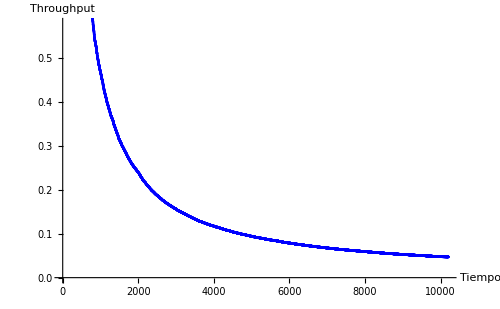
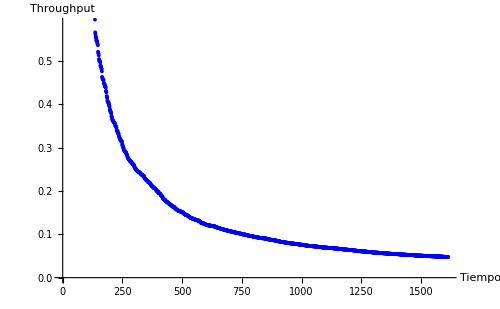
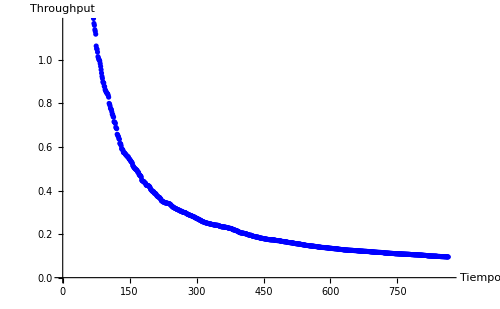
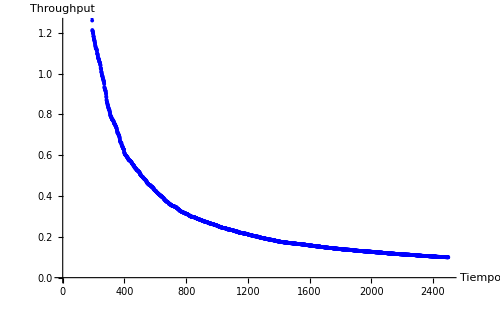
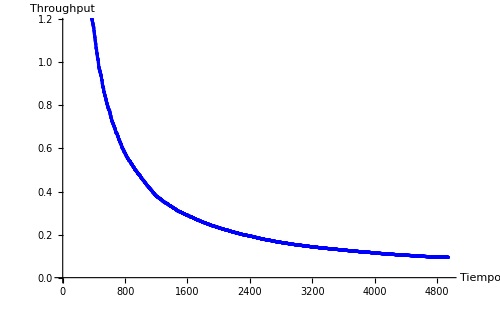
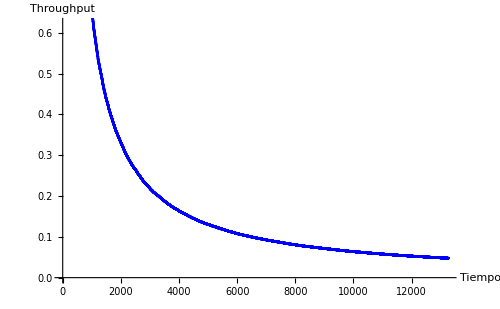
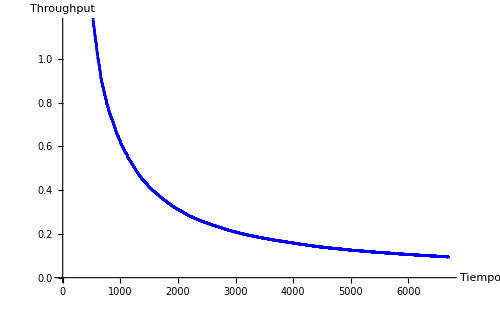
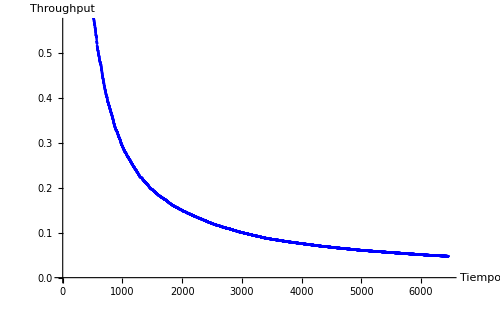
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-2-3"];

grafica2=Labeled[ListPlot[ThroughputList[paquetes1523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-2-3"];

grafica3=Labeled[ListPlot[ThroughputList[paquetes1524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-2-4"];

grafica4=Labeled[ListPlot[ThroughputList[paquetes154],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-4"];

grafica5=Labeled[ListPlot[ThroughputList[paquetes124],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-2-4"];

grafica6=Labeled[ListPlot[ThroughputList[paquetes23],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 2-3"];

grafica7=Labeled[ListPlot[ThroughputList[paquetes24],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 2-4"];

grafica8=Labeled[ListPlot[ThroughputList[paquetes523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-2-3"];

grafica9=Labeled[ListPlot[ThroughputList[paquetes524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-2-4"];

grafica10=Labeled[ListPlot[ThroughputList[paquetes54],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10
```

# 7B.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo S&W

```mathematica
(*Ejecución de la función*)
opcionesDistintas3SW=ObtenerOpcionesDistintas[out3SW]
opcionesDistintas4SW=ObtenerOpcionesDistintas[out4SW]

paquetes123SW = getPacketsWithRoute[out3SW,{"Ori-1",2,3}];
paquetes1523SW = getPacketsWithRoute[out3SW,{"Ori-1",5,2,3}];
paquetes1524SW = getPacketsWithRoute[out4SW,{"Ori-1",5,2,4}];
paquetes154SW = getPacketsWithRoute[out4SW,{"Ori-1",5,4}];
paquetes124SW = getPacketsWithRoute[out4SW,{"Ori-1",2,4}]; 
paquetes23SW= getPacketsWithRoute[out3SW,{"Ori-2",2,3}];
paquetes24SW = getPacketsWithRoute[out4SW,{"Ori-2",2,4}]; 
paquetes523SW = getPacketsWithRoute[out3SW,{"Ori-5",5,2,3}];
paquetes524SW = getPacketsWithRoute[out4SW,{"Ori-5",5,2,4}]; 
paquetes54SW = getPacketsWithRoute[out4SW,{"Ori-5",5,4}]; 

tot1SW = Length[out3SW]+Length[out4SW]
tot2SW = Length[paquetes123SW]+ Length[paquetes1523SW]+Length[paquetes154SW]+Length[paquetes1524SW]+ Length[paquetes124SW]+Length[paquetes23SW]+Length[paquetes24SW]+Length[paquetes523SW]+Length[paquetes524SW]+Length[paquetes54SW]
```

{{Ori-1,2,3},{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3}}

{{Ori-5,5,2,4},{Ori-5,5,4},{Ori-2,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-1,5,2,4}}

59980

59980

```mathematica
t123 = getRetardo[paquetes123SW]
t124= getRetardo[paquetes124SW]
t1523 = getRetardo[paquetes1523SW]
t1524 = getRetardo[paquetes1524SW]
t154 = getRetardo[paquetes154SW]
t23 = getRetardo[paquetes23SW]
t24 = getRetardo[paquetes24SW]
t523 = getRetardo[paquetes523SW]
t524 = getRetardo[paquetes524SW]
t54 = getRetardo[paquetes54SW]
```

2.35283

9.79891

1.22264

7.78841

0.317622

1.02854

7.32668

1.28538

7.70754

0.313823

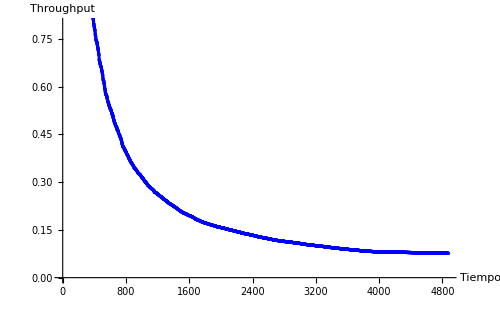
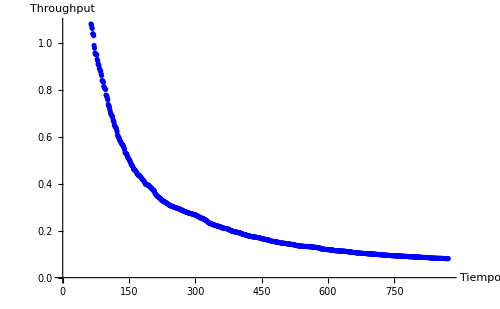
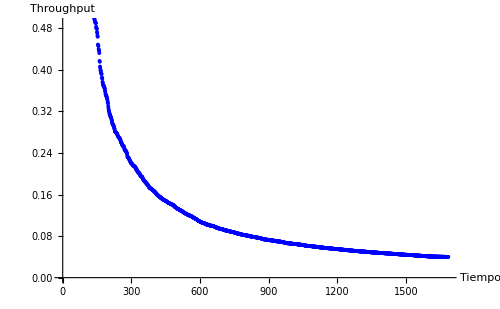
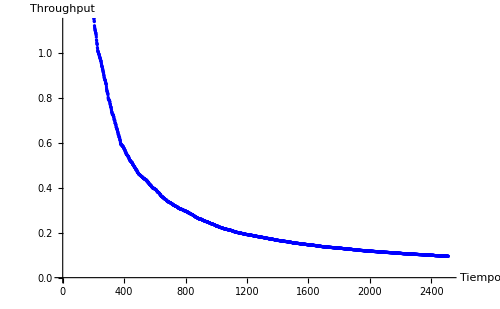
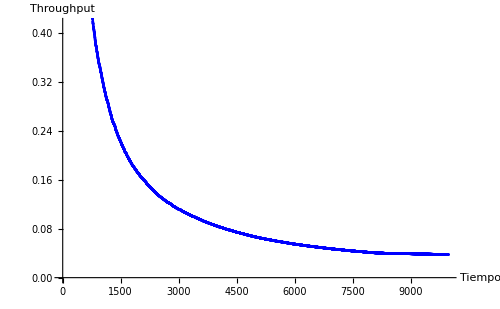
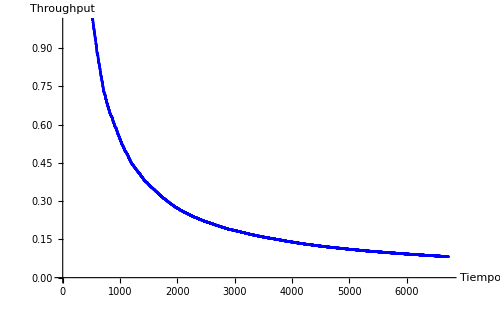
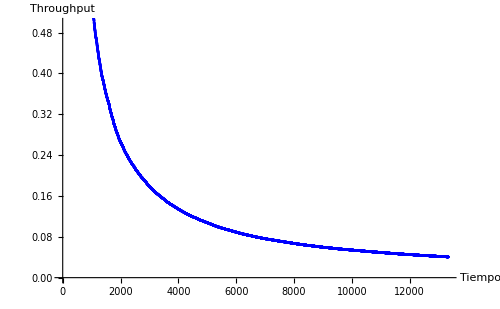
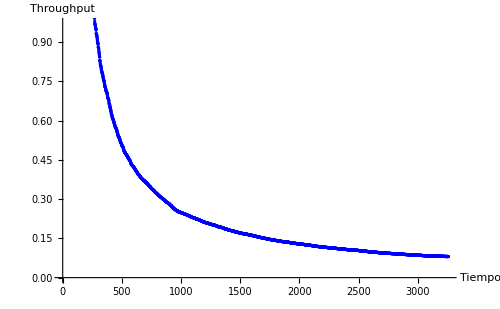
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10SW=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10SW
```

# 7C.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo GBN

```mathematica
(*Ejecución de la función*)
opcionesDistintas3GBN=ObtenerOpcionesDistintas[out3GBN]
opcionesDistintas4GBN=ObtenerOpcionesDistintas[out4GBN]

paquetes123GBN = getPacketsWithRoute[out3GBN,{"Ori-1",2,3}];
paquetes1523GBN = getPacketsWithRoute[out3GBN,{"Ori-1",5,2,3}];
paquetes1524GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,2,4}];
paquetes154GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,4}];
paquetes124GBN = getPacketsWithRoute[out4GBN,{"Ori-1",2,4}]; 
paquetes23GBN= getPacketsWithRoute[out3GBN,{"Ori-2",2,3}];
paquetes24GBN = getPacketsWithRoute[out4GBN,{"Ori-2",2,4}]; 
paquetes523GBN = getPacketsWithRoute[out3GBN,{"Ori-5",5,2,3}];
paquetes524GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,2,4}]; 
paquetes54GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,4}]; 

tot1GBN = Length[out3GBN]+Length[out4GBN]
tot2GBN = Length[paquetes123GBN]+ Length[paquetes1523GBN]+Length[paquetes154GBN]+Length[paquetes1524GBN]+ Length[paquetes124GBN]+Length[paquetes23GBN]+Length[paquetes24GBN]+Length[paquetes523GBN]+Length[paquetes524GBN]+Length[paquetes54GBN]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,2,3},{Ori-1,5,2,3}}

{{Ori-1,2,4},{Ori-2,2,4},{Ori-1,5,4},{Ori-5,5,4},{Ori-1,5,2,4},{Ori-5,5,2,4}}

59948

59948

```mathematica
t123 = getRetardo[paquetes123GBN]
t124= getRetardo[paquetes124GBN]
t1523 = getRetardo[paquetes1523GBN]
t1524 = getRetardo[paquetes1524GBN]
t154 = getRetardo[paquetes154GBN]
t23 = getRetardo[paquetes23GBN]
t24 = getRetardo[paquetes24GBN]
t523 = getRetardo[paquetes523GBN]
t524 = getRetardo[paquetes524GBN]
t54 = getRetardo[paquetes54GBN]
```

0.00302366

2.13014

0.0103773

2.1311

0.00767787

0.00212665

2.12453

0.00778836

2.11791

0.00515064

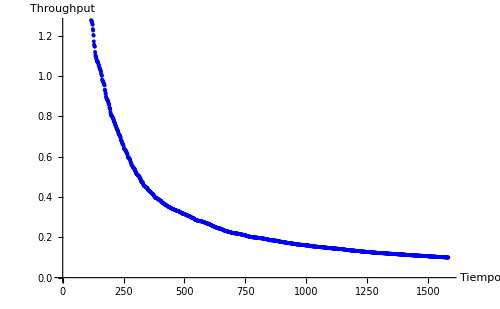
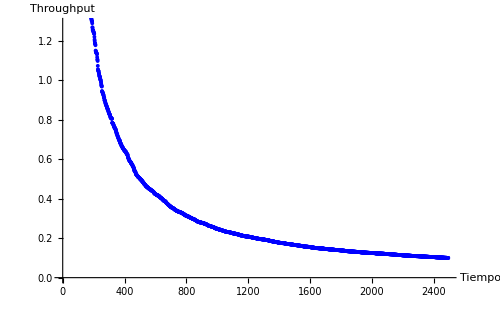
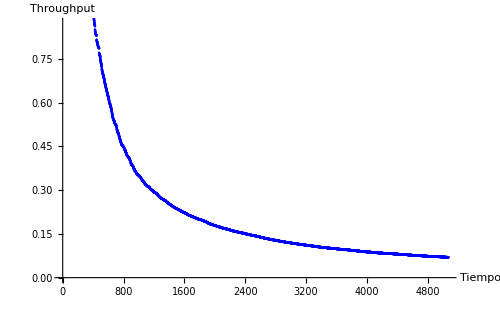
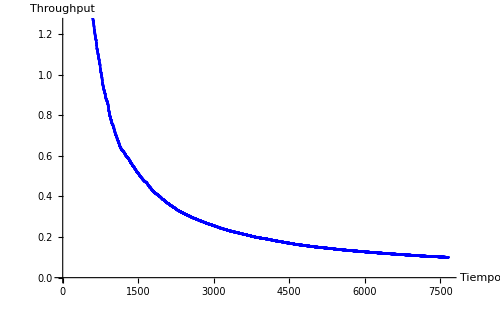
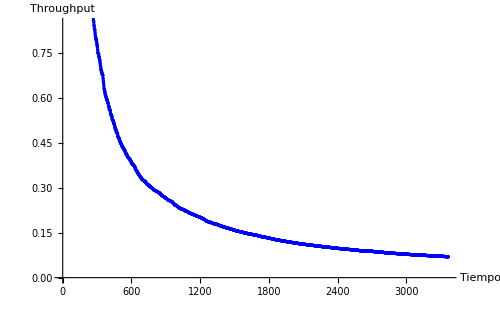
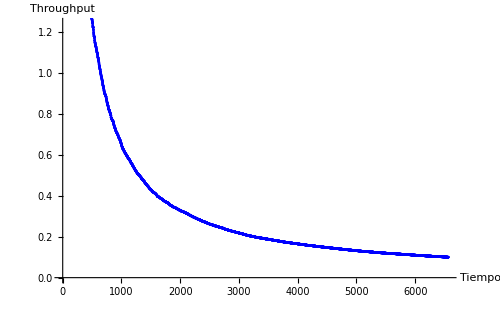
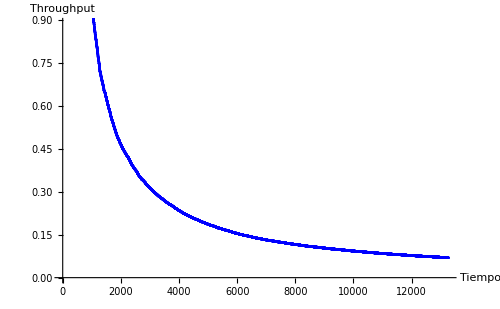
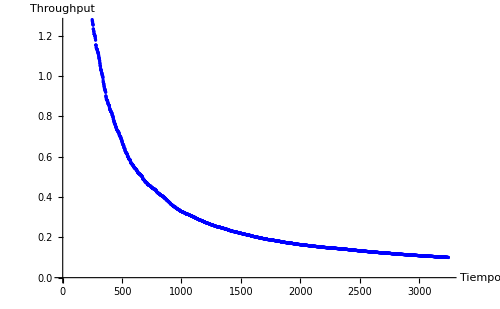
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"Tiempo","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10GBN=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10GBN
```